Oct 27 2010

## A parameterized sawtooth function, g

```mathematica
Clear["Global`*"]
```

```mathematica
g[t_,OptionsPattern[
{A->1,T->1,t1->0,t2->1/2}
]]:=Module[
{
A=OptionValue[A],
T=OptionValue[T],
t1=OptionValue[t1],
t2=OptionValue[t2],
tt,
tt2
},
If[t1>t2,
{t1,t2,A}={t2,t1,-A};
];
tt:=Mod[t-t1,T];(* periodic, translated time, so that t=t1 corresponds with tt=0*)
tt2 := t2 - t1;
Piecewise[{{-A+tt (2A)/tt2, 0≤ tt<tt2}, {A-(tt-tt2)(2A)/(T-tt2), tt2≤tt<T}}]
]
```

## A parameterized block wave function, b

```mathematica
b[t_,OptionsPattern[
{T->1,t1->0,t2->1/2}
]]:=Module[
{
T=OptionValue[T],
t1=OptionValue[t1],
t2=OptionValue[t2],
tt
},
tt=Mod[t,T];
If[t1>t2,
{t1,t2}={t2,t1};
];
Piecewise[{{0, 0≤ tt<t1}, {1, t1≤tt<t2}, {0, t2≤tt<T}}]
]
```

## Comparing the sawtooth and the triangular wave

```mathematica
Manipulate[
Plot[
{
O1+g[t,A->A1],
O2+g[t-mtd,A->A2,t1->mt1,t2->mt2],
-3+1/4 Sign[
O2+g[t-mtd,A->A2,t1->mt1,t2->mt2] -O1- g[t,A->A1]
]
},
{t,-1/2,3/2}, 
PlotRange ->{-4,3},
Ticks->{
{{-2,"-2T"},{-1,"-T"},{1,"T"},{2,"2T"},mt1,mt2},
{{-A1,"-A1"},{A1,"A1"},{-A2,"-A2"},{A2,"A2"}}
},
GridLines->{
{-2,-1,{1,Directive[Thickness[0.004],Black]},2,1/4,1/2},
{-A1,-A2,A1,A2}
},
GridLinesStyle->Directive[RGBColor[0.9,0.9,0.9],Dashed],
PlotStyle -> {
{Thickness[0.004]},
{Thickness[0.004]},
{Thickness[0.004]},
{Thickness[0.004]}
},
ImageSize->800
],
{{mt1,0},0,1},
{{mt2,1/2},0,1},
{{mtd,0},0,1},
{{A1,2},0,3},
{{A2,1},0,3},
{{O1,0},-3,3},
{{O2,0},-3,3}
]
```

## Integrating a rectangular wave

```mathematica
bi[t_]:=∫_(1/4)^t (0.1+-1+2b[τ])ⅆτ
```

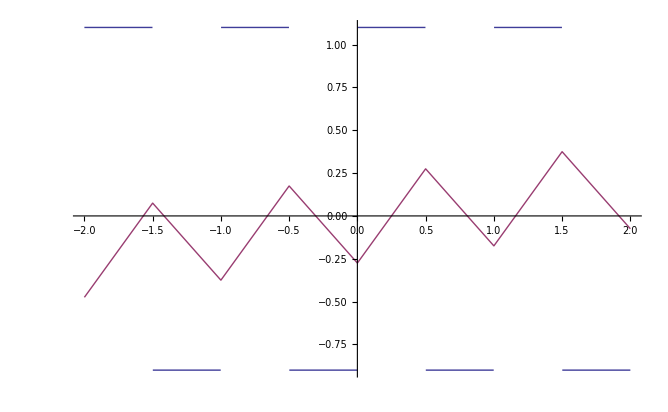

```mathematica
Plot[{0.1+-1+2b[t],bi[t]},{t,-2,2}]
```

## Integrating a sawtooth wave

```mathematica
Manipulate[
Plot[
{
g[t,t1->mt1,t2->mt2],
NIntegrate[g[τ,t1->mt1,t2->mt2],{τ,0,t}]
},{t,-2,2},
PlotStyle->{
{Thickness[0.005],Black},
{Thickness[0.005],Red}
}
],
{{mt1,0.3},0,1},
{{mt2,0.6},0,1}
]
```

## Fitting triangular waves

```mathematica
w[t_,OptionsPattern[
{t1->0,t2->1/2,T->1,v1->0,v2->1}
]]:=
Module[
{tt},
tt=Mod[t,T];
Piecewise[{{v2+(tt+(T-t2))(v1-v2)/(t1+(T-t2)), 0≤tt<t1}, {v1+(tt-t1)(v2-v1)/(t2-t1), t1≤tt<t2}, {v2+(tt-t2)(v1-v2)/(T+t1-t2), t2≤tt<T}}]
]
```

```mathematica
Manipulate[
Plot[{
g[t],
w[t,
t1->mt1,
t2->mt2,
v1->g[mt1],
v2->g[mt2],
]
},{t,-2,2},
PlotStyle->{
{Thickness[0.005],Black},
{Thickness[0.005],Red}
}
],
{{mt1,0},0,1},
{{mt2,1/2},0,1}
]
```

```mathematica
Plot[w,{{w
```